```mathematica
allGraphs4AtomKeys=Select[Keys[allGraphs4],Length[ListofVars[ allGraphs4[#,"colofour"]]]==1&]
```

{364,365,367,373,377,391,400,445,448,473,607,608,637,697,728}

```mathematica
repBase4=Table[allGraphs4[k,"colofour"]->Graph[allGraphs4[k,"graph"],ImageSize->{40,40}],{k,allGraphs4AtomKeys}]
```

{v1x2x3x4→-Graphics-,v1x2x34→-Graphics-,v1x24x3→-Graphics-,v1x23x4→-Graphics-,v1x234→-Graphics-,v14x2x3→-Graphics-,v14x23→-Graphics-,v13x2x4→-Graphics-,v13x24→-Graphics-,v134x2→-Graphics-,v12x3x4→-Graphics-,v12x34→-Graphics-,v124x3→-Graphics-,v123x4→-Graphics-,v1234→-Graphics-}

```mathematica
repNullBase4=Table[allGraphs4[k,"colofourrealnull"]->Graph[allGraphs4[k,"graph"],ImageSize->{40,40}],{k,allGraphs4NullAtomKeys}]
```

{n1x2x3x4→-Graphics-,n12x3x4→-Graphics-,n123x4→-Graphics-,n1234→-Graphics-,n124x3→-Graphics-,n12x34→-Graphics-,n13x2x4→-Graphics-,n134x2→-Graphics-,n13x24→-Graphics-,n14x2x3→-Graphics-,n14x23→-Graphics-,n1x23x4→-Graphics-,n1x234→-Graphics-,n1x24x3→-Graphics-,n1x2x34→-Graphics-}

```mathematica
repNullBase4Normal=Table[allGraphs4[k,"colofourrealnull"]->allGraphs4[k,"colofour"],{k,allGraphs4NullAtomKeys}]
```

{n1x2x3x4→v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4,n12x3x4→v1234+v123x4+v124x3+v12x34+v12x3x4,n123x4→v1234+v123x4,n1234→v1234,n124x3→v1234+v124x3,n12x34→v1234+v12x34,n13x2x4→v1234+v123x4+v134x2+v13x24+v13x2x4,n134x2→v1234+v134x2,n13x24→v1234+v13x24,n14x2x3→v1234+v124x3+v134x2+v14x23+v14x2x3,n14x23→v1234+v14x23,n1x23x4→v1234+v123x4+v14x23+v1x234+v1x23x4,n1x234→v1234+v1x234,n1x24x3→v1234+v124x3+v13x24+v1x234+v1x24x3,n1x2x34→v1234+v12x34+v134x2+v1x234+v1x2x34}

```mathematica
Table[
{Length[ListofVars[allGraphs4[k,"colofourrealnull"]]],allGraphs4[k,"colofour"],allGraphs4[k,"graph"]<->allGraphs4[k,"colofourrealnull"]/.repNullBase4}
,{k,allGraphs4AtomKeys}
]//Sort//TableForm
```

1 | v1234 | -Graphics-<->-Graphics-
2 | v123x4 | -Graphics-<->--Graphics-+-Graphics-
2 | v124x3 | -Graphics-<->--Graphics-+-Graphics-
2 | v12x34 | -Graphics-<->--Graphics-+-Graphics-
2 | v134x2 | -Graphics-<->--Graphics-+-Graphics-
2 | v13x24 | -Graphics-<->--Graphics-+-Graphics-
2 | v14x23 | -Graphics-<->--Graphics-+-Graphics-
2 | v1x234 | -Graphics-<->--Graphics-+-Graphics-
5 | v12x3x4 | -Graphics-<->2 -Graphics---Graphics---Graphics---Graphics-+-Graphics-
5 | v13x2x4 | -Graphics-<->2 -Graphics---Graphics---Graphics---Graphics-+-Graphics-
5 | v14x2x3 | -Graphics-<->2 -Graphics---Graphics---Graphics---Graphics-+-Graphics-
5 | v1x23x4 | -Graphics-<->2 -Graphics---Graphics---Graphics---Graphics-+-Graphics-
5 | v1x24x3 | -Graphics-<->2 -Graphics---Graphics---Graphics---Graphics-+-Graphics-
5 | v1x2x34 | -Graphics-<->2 -Graphics---Graphics---Graphics---Graphics-+-Graphics-
15 | v1x2x3x4 | -Graphics-<->-6 -Graphics-+2 -Graphics-+-Graphics-+2 -Graphics-+2 -Graphics-+-Graphics-+2 -Graphics-+-Graphics---Graphics---Graphics---Graphics---Graphics---Graphics---Graphics-+-Graphics-

```mathematica
Table[
{Length[ListofVars[allGraphs4[k,"colofour"]]],allGraphs4[k,"colofourrealnull"],allGraphs4[k,"graph"]<->allGraphs4[k,"colofour"]/.repBase4}
,{k,allGraphs4NullAtomKeys}
]//Sort//TableForm
```

1 | n1234 | -Graphics-<->-Graphics-
2 | n123x4 | -Graphics-<->-Graphics-+-Graphics-
2 | n124x3 | -Graphics-<->-Graphics-+-Graphics-
2 | n12x34 | -Graphics-<->-Graphics-+-Graphics-
2 | n134x2 | -Graphics-<->-Graphics-+-Graphics-
2 | n13x24 | -Graphics-<->-Graphics-+-Graphics-
2 | n14x23 | -Graphics-<->-Graphics-+-Graphics-
2 | n1x234 | -Graphics-<->-Graphics-+-Graphics-
5 | n12x3x4 | -Graphics-<->-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
5 | n13x2x4 | -Graphics-<->-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
5 | n14x2x3 | -Graphics-<->-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
5 | n1x23x4 | -Graphics-<->-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
5 | n1x24x3 | -Graphics-<->-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
5 | n1x2x34 | -Graphics-<->-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
15 | n1x2x3x4 | -Graphics-<->-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

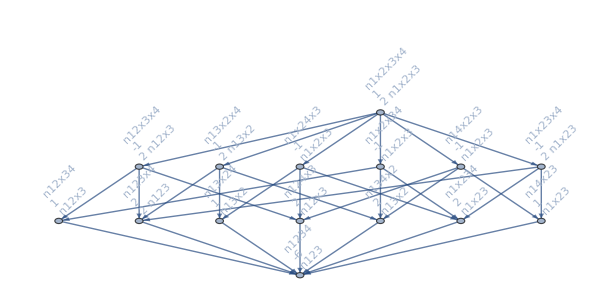

```mathematica
MobiusGraph4[K4Key,allGraphs4]
```